## MICA: Measurement, Instrumentation, Control & Analysis

## Operational Amplifiers

#### Ariel Mobius, 28 April 2026

#### Revisions

2025		Oct	 6	Adapted from earlier notes in MathCad 	
2026		Apr	25	Updated with power amps and general op amp recommendations

#### Objectives

To explain the history and basic operation of operational amplifiers (op amps). To recommend useful op amps for particular applications.

#### Keywords

Operational Amplifier, Op Amp, 741 Op Amp, Gain, Phase, Inverting Amplifier, Non-Inverting Amplifier, Frequency Response, Bode Plot, Cut-Off Frequency, Resistor, Capacitor, Spec Sheet, Swept Sine Testing, Step Response, Impulse Response, Transfer Function, Common Mode Rejection Ratio (CMRR), Power Supply Rejection Ratio (PSRR), Small Signal Bandwidth, Large Signal Bandwidth, Slew Rate Limit,  Power Op Amp, High Voltage Op Amp, Chopper Stabilized Op Amps, FTE Input Op Amps

#### Background

The integrated circuit (IC) operational amplifier (Op Amp) is the building block for many analog electronic circuits. They are used extensively in analog control systems and in sensor electronics. An operational amplifier is a very high gain amplifier with a pair of differential inputs (one positive and one negative). By feeding back the output of an op amp to its negative input in various ways (i.e. via combinations of capacitors, resistors and inductors) a remarkably wide range of capabilities can be achieved.

-Graphics-
Harold Black invented the negative feedback amplifier in 1927 at Bell Labs.
“He paved the way for routine long-distance telephone service by eliminating distortions that could reduce to gibberish the sound of a phone call amplified over and over again on its way across the country.” From http://www.alcatel-lucent.com

Ideal op amps have an infinite gain. In practice the open-loop gain is typically in range of  10^6 to 10^7. In an ideal op amp no current flows in to either input (i.e. they are entirely voltage controlled and have infinite input impedance). In practice the input impedances are typically in the  10^8 to 10^12 Ω range and have offset and bias currents in the nA range (in very special purpose op amps the input and bias currents can be in the fA range). Ideal op amps act as pure voltage sources (i.e., they can be modeled as a Thevenin source with very low output impedance). In reality op amps typically have open-loop output impedances in the Ω range (and closed-loop output impedances in the mΩ range) and output offsets (due to a variety of internal design factors) in the 10 μV to 1 mV range (the output offset voltage also drifts with temperature changes). Most op amps provide offset trimming capabilities to null the output (set it to zero for zero input). 

Op amps can typically function using a range of supply voltages (e.g., ±5 V to ±18 V depending on the type). The input voltages can usually go to within 2 V of the supply voltage. Indeed some op amps can operate from a single supply voltage. The output of common op amps can only drive low currents (e.g., 10 mA). However special purpose high current output op amps (called power op amps) are available with output drive capabilities to 50 A. Another class of special purpose op amps is available for high voltage applications (e.g., driving piezoelectric actuators) and can deliver up to ±1500 V.

Ideal op amps have an infinite open-loop bandwidth. In practice the closed-loop bandwidth is dependent on the feedback gain (the higher the gain the lower the bandwidth). For this reason the op amp data sheet will always specify its gain bandwidth product (e.g., 1 MHz (i.e. for a gain of 10 the bandwidth would extend from 0 to 100 kHz)). 

Although op amps may be considered to be dynamically linear devices under many conditions they do display some nonlinear behavior. The major nonlinearity is an op amps “slew rate” limit. This is the maximum achievable change in output voltage per unit time. Typical precision op amps have slew-rate limits in the order of 10^6  V/s . Op amps used in high performance video systems need to achieve much higher slew-rates. The slew-rate limit is the reason why the bandwidth of an op amp is wider for small signals than large. For this reason it is common for op amp spec sheets to specify both the small signal and large signal responses. 

The degree to which an op amp is able to perform the subtraction of the inverting input from the non-inverting input is measured by its common mode rejection ratio (CMRR). CMRR is discussed in detail in a subsequent section on instrumentation amplifiers. A typical modern op amp will have a common mode rejection ratio in the order of 10^6 to 10^7. 

Another important op amp specification is the power supply rejection ratio (PSRR). Early op amps had very little ability to reject power supply variations (e.g., as caused by batteries running down). Modern op amps are typically able to attenuate the effect of power supply changes by as much as 10^7 times  (10^5 typical). The op amp spec sheet usually specifies both the CMRR and PSRR in dB (e.g., 10^7 is 140 dB). 

Modern op amps are low noise devices. The total output voltage noise increases with bandwidth (for this reason you should limit the bandwidth of an op amp to the frequency range of interest). Op amp spec sheets usually specify a peak-to-peak voltage noise at low frequencies and a noise density (in V/√Hz) at higher bandwidths. 

There are 1000s of different op amps available. One of the first popular op amps in chip form was (and is) called the 741 and is usually sold as a chip with 8 legs (called an 8 pin DIP (dual inline package)). Many op amps follow the pin out of the original 741 op amp which is shown on the left below. Many modern op amps use a slightly different pin-out as shown below right. If output nulling is not required then the offset trim pins are simply left disconnected. Unlike the classic 741 many modern op amps will survive a brief accidental inversion of the supply voltage polarity.

-Graphics-

The orientation (e.g., location of pin 1) of an op amp is typically indicated by a recessed dot or notch as shown above). In the past op amps were mounted on printed circuit boards (PCBs) using PCB through holes. The PCBs usually were 2 sided (i.e., had conductive copper traces on each side). Transistors, resistors, capacitors, inductors, diodes, op amps (and other ICs) were normally laid out on a 0.1 inch spaced grid (that is why DIP style op amps and other ICs have adjacent legs (pins) spaced 0.1 inch apart). Modern PCBs have multiple internal layers (e.g., 12 layers) and the electronic components are now mounted on the top and bottom surface of a PCB by special purpose precision robots call “pick and place” machines. Attaching all the components on a printed circuit board is call “populating “ the PCB. Such surface-mount components are now much smaller and no longer have 0.1 inch spaced legs.

#### Follower (Buffer, Unity Gain Amplifier)

The following circuit is often used to isolate one circuit from another.

-Graphics-

V_out  = V_in

The open-loop gain, G_(open loop), of a modern op-amp is typically  >10^6

The closed-loop gain, G_(closed loop), of a modern op-amp is = (G_(open loop))/(1+G_(open loop)) which is very close to 1.
Therefore we say that the output “follows” the input.

#### Non Inverting Amplifier

-Graphics-

V_out  = (1+R1/R2)V_in

Note that the close-loop gain is always > 1

Note that a highly undesirable consequence of using this circuit is that the output will usually swing to near the positive or negative supply when nothing is connected to the input. To avoid this a high value resistor (> 10^6 Ω) is often put between the positive input and ground.

#### Inverting Amplifier

-Graphics-

V_out  = -R1/R2 V_in

Note that the magnitude of the gain can be greater than 1, equal to 1 (if R1 = R2) or less than 1.

#### Variable Gain (from -1 to 1) Amplifier

Sometimes it is necessary to attenuate a signal with a gain which between -1 and 1. The following simple yet beautiful circuit achieves this.

-Graphics-

R is commonly some value between 10 kΩ and 100 kΩ.

#### Summing Amplifier

-Graphics--Graphics-

V_out  =  -(V1_in + V2_in + V3_in)

R is commonly some value between 10 kΩ and 100 kΩ.

#### Adding an Offset

The summing circuit above can be used to add an offset to a signal. A common mistake is to use the power supply to provide a voltage which is then divided down to a desired value by a potentiometer (variable resistor). Any noise in the power supply is then undesirably passed on to the signal. A better approach is to use a precision voltage reference which is a special purpose chip designed to produce a very stable and low noise voltage (e.g., 10 V) as shown below.

-Graphics--Graphics-

V_out  =  -(V_in + V_offset)

R is commonly some value between 10 kΩ and 100 kΩ.

A good general purpose 10 V precision voltage reference is the Ref01 made by Analog Devices.
A selection of different types of voltage references is given at the end of these notes.

#### Differential (Subtraction) Amplifier

-Graphics--Graphics-

V_out  =  V2_in - V1_in

R is commonly some value between 10 kΩ and 100 kΩ.

The resistors need to be very closely matched (e.g., to within 0.01%) to achieve precise subtraction. The common mode rejection ratio, CMRR, specifies the success with which the subtraction amplifier suppresses noise which is common to both inputs. This topic is treated again when instrumentation amplifiers are considered.

A slight modification of the circuit above enables subtraction with gain as shown below.

-Graphics-

V_out  = R1/R2 (V2_in - V1_in)

#### Input Buffered Differential Amplifier

It is often a good idea to isolate the differential amplifier from previous circuit elements such as sensors. This may be achieved by adding a unity gain buffer in front of each input to the circuit as shown below.

-Graphics-

V_out  = V2_in - V1_in

#### Instrumentation Amplifier

The design above has a number of disadvantages. Firstly, the buffers do not contribute to the subtraction and so all the common mode rejection is carried out by the last op-amp with result (as stated before) that the resistors have to be matched to great accuracy (and remain matched with temperature changes and time). Secondly, the configuration above has unity gain. In many applications it is desirable to be able to reject common mode noise while also amplifying the signal. The following circuit has a specifiable gain and also uses the first op-amps to do some of the common mode rejection. The matching of the resistors associated with the last op-amp is as a consequence less critical. This very elegant three op-amp circuit forms what is called an instrumentation amplifier. Such amplifiers are used extensively in instrumentation and are available in single chip packages in which the instrumentation amplifier gain is set by one external resistor, RG.

-Graphics-

V_out  = G (V2_in - V1_in)

where the instrumentation amplifier gain, G is

G = 1 + 2 R/(^R G)

A good general purpose low cost instrumentation amplifier is the Amp02 made by Analog Devices.
The Amp02 has a common mode rejection ratio (CMRR) of nearly 10^6 at low frequencies.
A selection of suggested instrumentation amps is given near the end of these notes.

#### First-Order Low-Pass Filter

The inverting amplifier may be modified into a first-order, low-pass filter by the addition of a capacitor in the feedback loop.

-Graphics-

The static (low-frequency) gain is given by  G = R1/R2  and the time constant, τ  = R1 C

The cut-off frequency, (frequency at which the gain is G/(√2)  =  0.7071 G    or  3 dB down)   =   1/τ rads/s
The transfer function is 
H(s) = G/(τ s + 1)

For example if  R1  = 100 kΩ ,  R2 = 10 kΩ,   C = 10 nF  then  G = -R1/R2 = -10   and  τ = R1 C = 10^-3s  =  1 ms

The transfer function is  H(s) = G/(τ s + 1)  = 5/(0.001 s +1)

Note that because the gain is negative (remember this low-pass filter design is a modification of the inverting amplifier) the phase starts at 180 instead of 0 deg.

The general equation for the transfer function of a first-order low-pass filter is:

```mathematica
"■"; H[s_,α_,ω_]:=(α ω)/(s+ω);
```

where the static gain is α, the “cut-off” frequency (in radians/s) is ω = 1/τ.

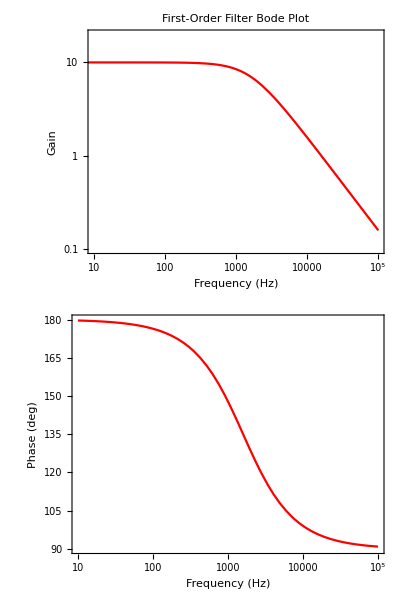

```mathematica
"■";
Column[
{LogLogPlot[Abs[H[ⅈ f 2 π,-10,10000]],{f,1,100000},PlotRange->{{10, 100000},{0.1,20}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"First-Order Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->600],
LogLinearPlot[360/(2*Pi)Arg[H[ⅈ f 2 π,-10,10000]],{f,10,100000},PlotRange->{{10, 100000},{90,180}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->600]},
Spacings->0]
```

Note that the natural frequency, ω, is in radians/s (divide by 2 π   to get the natural frequency in Hz).

#### Second-Order Filters

There is a remarkable op amp circuit, called a Sallen-Key filter, which implements a second-order filter (either low-pass, high-pass, band-pass or notch) and has the following general circuit:

-Graphics-

where Z1, Z2, Z3 and Z4 can each be any parallel or series combination of resistors, capacitors and inductors. By choosing what Z1, Z2, Z3, and Z4 are we can design a variety of second-order filters (low-pass, high-pass, band-pass and band-stop).
From https://upload.wikimedia.org/wikipedia/commons/e/e3/Sallen-Key_Generic _Circuit.svg
The general transfer function is:
tf[s_]:=(z3[s]z4[s])/(z1[s] z2[s] +z3[s](z1[s]+z2[s]) + z3[s] z4[s])

tf[s]
(z3[s] z4[s])/(z1[s] z2[s]+(z1[s]+z2[s]) z3[s]+z3[s] z4[s])

Normally you need 2 op amps to create a second-order filter but the Sallen-Key design only needs 1 op amp and it has a positive gain (i.e. non-inverting).

#### Second-Order Low-pass Sallen-Key Filter

For the case of a second-order, low-pass, filter where we want to have a specified static gain and a specified damping parameter we need to add a few more components:

In order to achieve the desired α, ω, and ζ using standard precision resistors and capacitors we typically have to use two capacitors in series to get the desired capacitance (because like resistors and inductors, capacitors only come in a limited range of values).

There are a few ways we can choose the values of the components to get the desired static gain, α, natural frequency (in rad/s) ω and damping parameter, ζ. 
We can choose a design where the capacitors are equal as follows:    C1a =  C2a  ≡  Ca   and    C1b =  C2b  ≡  Cb

The transfer function will have the form of a second-order, low-pass, transfer function:

```mathematica
"■"; tf[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2ζ ω s+ω^2)
```

Lets say we want   α = 2, ω = 2π rad/s (i.e. 1 kHz), and ζ = 0.3 then we could use:

```mathematica
"■"; 
R1=50. 10^3; (* 50 kΩ *)
R2=18. 10^3; (* 18 kΩ *)
R3=10. 10^3; (* 10 kΩ *)
R4=10. 10^3; (* 10 kΩ *)
Ca=8.2 10^-9; (* 8.2 nF *)
Cb= 15. 10^-9; (* 15 nF *)
Cab=(1/Ca+1/Cb)^-1   (* 8.2 nF in series with 15 nF = 5.3017 nF *)
```

5.30172×10^-9

We know the uncertainty of the components (resistors are ±0.1% and capacitors are ±1%) so we can include these in our calculations to give uncertainties in the α, ω, and ζ  parameters. We use the Mathematica function Around[] to do this. For example, if we have a 0.1% 1 kΩ resistor, R,  then we set:

```mathematica
R1=Around[1. 10^3,0.001 1. 10^3] (* 1 kΩ ±0.1% *)
```

1000.01.0

This gives the expected 1,000 Ω  ± 1 Ω. because 0.1% of 1,000 Ω is 1 Ω

```mathematica
"■"; 
R1=Around[50. 10^3,0.001 50. 10^3]; (* 50 kΩ ±0.1% *)
R2=Around[18. 10^3,0.001 18. 10^3]; (* 18 kΩ ±0.1% *)
R3=Around[10. 10^3,0.001 10. 10^3]; (* 10 kΩ ±0.1% *)
R4=Around[10. 10^3,0.001 10. 10^3]; (* 10 kΩ ±0.1% *)
Ca=Around[8.2 10^-9,0.01 8.2 10^-9]; (* 8.2 nF ±1% *)
Cb= Around[15. 10^-9,0.01 15. 10^-9]; (* 15 nF ±1% *)
Cab=(1/Ca+1/Cb)^-1   (* 8.2 nF in series with 15 nF = 5.3017 nF *)
```

5.300.0410^-9

then we get:

```mathematica
"■"; αα=1+R4/R3
```

2.00000.0014

and

```mathematica
"■"; ωω=1/(Cab √(R1 R2)) (* in rad/s *)
```

6287.47.

or

```mathematica
"■"; ωω/(2π) (* Hz *)
```

1001.7.

and

```mathematica
"■"; ζζ=1/2 √(R2/R1(3-αα))
```

0.300000.00030

These are amazingly close to the desired values! 
The resistor values used in the circuit are type metal film with 0.1% resistance tolerance and the capacitors are type ceramic with 1% capacitance tolerance. These are expensive components and result in circuits with less variation in α, ω, and ζ than usual.
For reference: metal film resistors are normally within around 1% and ceramic capacitors are normally within 5%.

#### Current to Voltage Converter

It is often the case that a sensor produces a current rather than a voltage. For example photo-diodes produce a current which is proportional to the incident light intensity. The following circuit converts this current in to a voltage.

-Graphics-

V_out  = i R

For example if   i = 10^-6 A   and if    R = 10^6 Ω   then   V_out  = i R  = 1 V

#### Active Half-Wave Rectifier

So far all of our circuits have contained linear elements (resistors, capacitors) and have implemented linear analog transformations (multiplication, addition, subtraction, filtering, etc). A common nonlinear operation is the rectifier.

The following circuit implements a half-wave rectifier.

-Graphics-

As you can see in this example (where the input is a sinusoid) the circuit sets all negative values of the input to zero (i.e., it only “passes” positive values).

We can simply reverse the diodes the get the negative portion of the input waveform (i.e., it only
“passes” negative values).

-Graphics-

#### Active Rectifier (Absolute Value)

Sometimes we need to implement a full-wave rectifier. A full-wave rectifier is the same as the absolute value function and transforms a sinusoid as:

-Graphics-

The following circuit implements a full-wave rectifier.

This is a very elegant circuit in which the first op amp half wave rectifies (negative values “passed”) Vin which is then multiplied by 2 and added to Vin by the second op amp with the result that Vout(t) = |Vin(t)| .

-Graphics-

#### General-purpose / precision op amps

These are the parts that show up repeatedly across instrumentation, lab equipment, and signal-conditioning circuits. The first table groups by application emphasis; specs are typical values from current data sheets.

#### Instrumentation amplifiers

Instrumentation amps (INA’s) are a much smaller market than op amps. The selection axes are: (1) gain-setting method (single resistor vs digitally programmable vs fixed), (2) input common-mode range relative to supply, (3) DC accuracy (Vₒₛ, drift, CMRR at gain), and (4) noise. The list below covers what’s actually used in the lab.

#### Specialty: the “indirect current feedback” architecture

These deserve a separate mention because they break the gain–CMRR tradeoff inherent in the classical three-op-amp INA topology. Worth knowing about:

	•	AD8295 — INA + two auxiliary op amps + matched resistors in one package (signal 				conditioning subsystem)
	•	AD8237 — micropower indirect current feedback, rail-to-rail input and output
	•	MAX4194 / MAX4197 — micropower, pin-compatible alternatives in the AD620 footprint

#### Practical recommendations for the Typical Labs

If I were stocking a single drawer, the parts that give 90% coverage are:

	•	OPA627 for high-Z FET-input precision work (photodiode amps, electrometer front-ends)
	•	OP27 / OPA211 for low-noise sensor preamps with bipolar inputs
	•	LTC2057 when DC accuracy matters more than bandwidth
	•	AD797 for the rare combination of low noise and high speed
	•	TL072 / OPA1642 for everyday bread boarding
	•	AD8221 or INA128 as the default INA
	•	AD8429 when input-referred noise matters (electrophysiology, low-frequency strain gauges)
	•	LTC2053 when DC accuracy in an INA matters (thermocouples, long-term drift)

#### Power Buffers

All the op amp circuits we have looked at so far would typically be built using op amps with limited current driving capabilities (typically around ±20 mA continuous and ±35 mA max). This is insufficient to drive motors, speakers, and lights (except for LEDs requiring <20 mA). There are two approaches you can take if you need more current. 
The first is to use a fast unity-gain buffer such as a LT1010 (Linear Technology, now Analog Devices) or equivalent which is designed to be placed inside the feedback loop of an op amp to extend its output current and speed without disturbing the loop dynamics. The LT1010 can drive ±150 mA continuous and ±200 mA max. 
For new designs that need more current or higher speed, you would now reach for:

	•	BUF634A (TI, 250 mA, 210 MHz) — closest direct replacement, with selectable bandwidth via a bias pin (same idea as LT1010).
	•	LT1206 / LT1210 (250 mA / 1.1 A current-feedback amplifiers) — when you also want gain.

These power buffers can be used inside the feedback loop of both the inverting and non-inverting op amp configurations shown earlier.

#### Power Op Amps

A better alternative is to use an op amp specifically designed to drive large currents. The OPA541 / OPA549 are the canonical “power op amp” parts to know (see 5 to 10 A class below).  They’re cheap enough to design with and well-documented. 
Most of these power op amps can be configured as inverting or non-inverting configurations as shown earlier in these notes. Some of them have additional terminals which are used to provide adjustable current limiting so that they, or what they are driving, are not over driven.

#### High Voltage Op Amps

High voltage output op amps are available and are useful for driving high voltage devices such as piezoelectric actuators.

#### Practical Voltage References

Here are some voltage reference suggestions for use in various applications: